```mathematica
computat
```

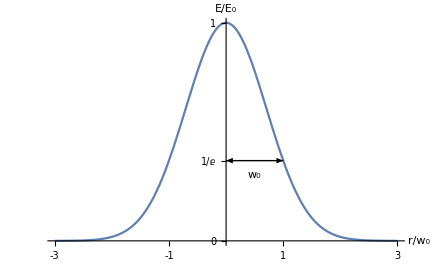

```mathematica
Show[{Plot[ⅇ^(-x^2),{x,-3,3},Axes->{Automatic,Automatic},AxesLabel->{"r/w_0","E/E_0"},Ticks->{{-3,-2,-1,0,1,2,3},{0,1/ⅇ,1}},AxesStyle->Directive["Label", 16]],Graphics[{
Style[Arrow[{{0,1/ⅇ},{1,1/ⅇ}}],Arrowheads[{-0.03,0.03}]],
Style[Text["w_0",{0.5,0.3}],FontSize->30]
}]}]
```

```mathematica
ⅇ^-1
```

1/ⅇ

```mathematica
ArcTan[0]
```

0

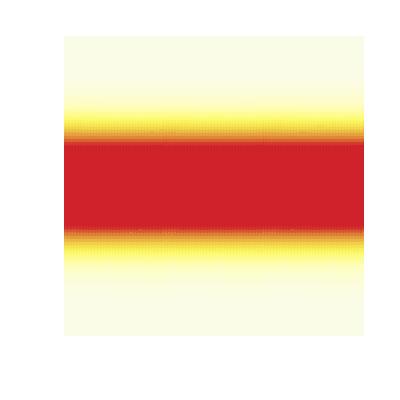

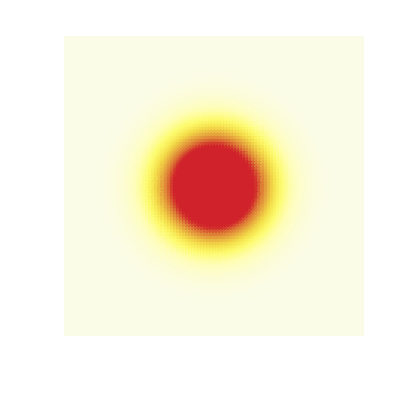

```mathematica
DensityPlot[0.5*ⅇ^(-x^2),{z,-3,3},{x,-3,3},Axes->False,AxesLabel->{"z","y"},Frame->False,Ticks->None,AxesStyle->Directive["Label", 16],ColorFunction->newFunction,Mesh->None,PlotPoints->100]
DensityPlot[0.2*ⅇ^(-(x^2+z^2)),{z,-3,3},{x,-3,3},Axes->False,AxesLabel->{"z","y"},Frame->False,Ticks->None,AxesStyle->Directive["Label", 16],ColorFunction->newFunction,Mesh->None,PlotPoints->100,PlotRange->Full]
```

```mathematica
ColorData["TemperatureMap"][0]
```

RGBColor[0.178927, 0.305394, 0.933501]

```mathematica
newFunction[x_]=ColorData["TemperatureMap"][x+0.5]
```

Blend[TemperatureMap,0.5+x]

```mathematica
newFunction[-0.5]
```

RGBColor[0.178927, 0.305394, 0.933501]

```mathematica
ColorData["TemperatureMap"][0.5]
```

RGBColor[0.984192, 0.987731, 0.911643]

```mathematica
0.5*ⅇ^(-(x^2+z^2))/.{x->0,z->0}
```

0.5